# Exploring the dimensionality of Wolfram Models as a function of the number of steps

Darya Dyachkova

Minerva Schools at KGI

## Abstract: The project is concerned with discovering correlations between the growth of dimensionality of the model with the number of steps applied. The first step is to categorize the rules based on whether they lead to increasing, decreasing or periodic relationships with the number of dimensions. Based on that information, it may be possible to study the connection to particle physics - to explore how the de Sitter entropy of the universe relates to the entropy of the graph. The results will also be relevant to study the correspondence between the evolution of the Wolfram models and early universe inflation models - to analyze the evolution of the quantum degrees of freedom as the universe was expanding.

## Initializing

```mathematica
<<SetReplace`
```

```mathematica
rules=Import["https://www.wolframcloud.com/obj/wolframphysics/Data/RuleEnumerations/22-32c.wxf"];
```

```mathematica
initStates={{{0,0},{0,0}},{{0,1},{1,0}},{{0,1},{1,2}},{{0,1},{0,2}},{{0,0},{0,1}},{{0,1},{0,1}},{{0,1},{2,1}},{{0,0},{1,0}}};
```

## Hausdorff

```mathematica
calcSlopeH[eo_] := Module[{rules},
rma = ResourceFunction["RaggedMeanAround"][Values[ResourceFunction["HypergraphNeighborhoodVolumes"][eo["FinalState"]]]];
p=Predict[Range[Length[rma]]-> rma,Method->"LinearRegression"];
pred = p[Range[Length[rma]]];
slope = (pred[[-1]] - pred[[1]])/Length[pred];
slope]
```

```mathematica
rulesEos[n_] := Module[{},
rulesRange = Range[n, n+100];
eos = Select[ParallelMap[WolframModel[#,{{0,0},{0,0}},9]&,rules[[rulesRange]]],Length[#["FinalState"]]>10&&ResourceFunction["ConnectedHypergraphQ"][#["FinalState"]]&];
eos]
```

```mathematica
calcSlopeFullH[n_] := Module[{},
eos = rulesEos[n]; 
slopes = Table[calcSlope[eos[[t]]], {t, 1, Length[eos]}];
slopes
]
```

## Spectral dimension

```mathematica
getTrMatrix [gr_] := Module[{},
adj = Normal[AdjacencyMatrix[gr]];
adjTr = adj + Transpose[adj];
adjNorm = Table[adjTr[[i]] / (adjTr[[i]] // Total), {i, 1, Length[adjTr]}]; 
adjNorm]
```

```mathematica
randWalkStep[i_, matrix_] := Module[{}, 
elements = Range[Length[matrix]];
probs =  matrix[[i]];
sample = RandomChoice[probs -> elements];
sample
 ]
```

```mathematica
randWalk[matrix_,start_]:= Module[{},
current = start; 
walk = List[];
count = 0 ;
If[Length[matrix] == 1, AppendTo[walk, 0]; Print["zero dim"]; Break[],
 While [True, sample = randWalkStep[current, matrix]; count ++; If[sample == start, AppendTo[walk, count]; Break[], current=sample]]];
walk];
```

```mathematica
randWalkGraph[state_]:= Module[{}, 
gr = ResourceFunction["HypergraphToGraph"][state];
center = Part[VertexList[IndexGraph[gr]],Ordering[RadialityCentrality[gr],All,Greater]][[1]];
adjM = getTrMatrix [gr];
If[Length[adjM] > 1,  
res = Flatten[Table[randWalk[getTrMatrix [gr] , center], {i, 1,1000}]];
Round[Mean[res]], 0
]]
```

```mathematica
calcSlopeRW[eo_] := Module[{rules},
rma = Table[randWalkGraph[eo["StatesList"][[i]]], {i, 2, Length[eo["StatesList"]]}];
Echo @ rma;
p=Predict[Range[Length[rma]]-> rma,Method->"LinearRegression"];
pred = p[Range[Length[rma]]]; 
slope = (pred[[-1]] - pred[[1]])/Length[pred];
slope]
```

```mathematica
calcSlopeFullRW[i_, j_, rulesApprovedNoNull_, rules_, initStates_] := Module[{}, 
initState = initStates[[i]];
rule = rules[[RandomChoice[rulesApprovedNoNull[[1]][[i]]]]];
Print[i, " ", j];
eo = ResourceFunction["WolframModel"][rule, initState, Automatic];
slope = calcSlopeRW[eo];
slope]
```

```mathematica
eoCheck[initState_, ruleInd_, rules_] := Module[{},
rule = rules[[ruleInd]];
eo = WolframModel[rule, initState, Automatic];
condition = Length[eo["FinalState"]]>10&&ResourceFunction["ConnectedHypergraphQ"][eo["FinalState"]];
If[condition, ruleInd]]
```

## Full sample

```mathematica
slopesFull = Table[calcSlopeFullRW[initStates[[i]], rules[[j]]],{i,1, Length[initStates]},{j,1, Length[rules]}];
```

```mathematica
Table[Show[Histogram[slopesFull[[i]], 20]], {i, 1, Length[initStates] }]
```

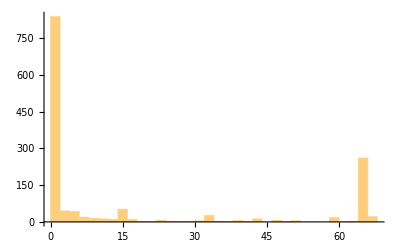
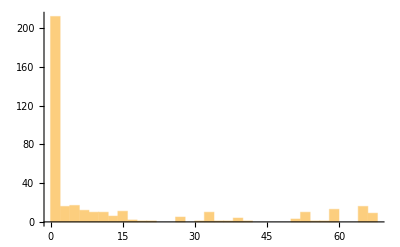
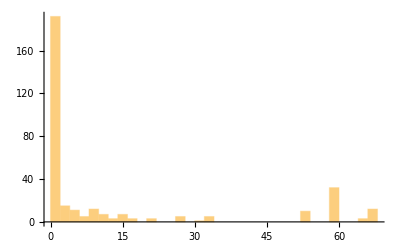
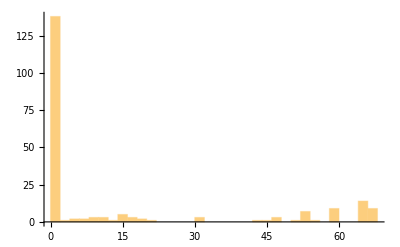
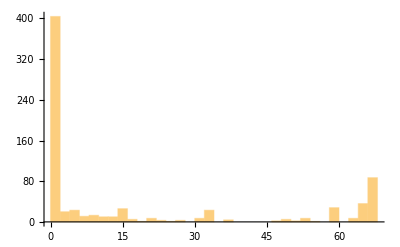
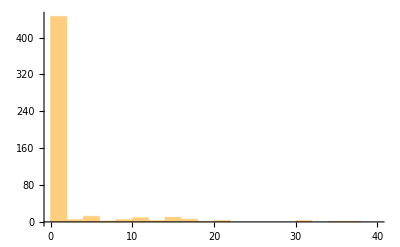
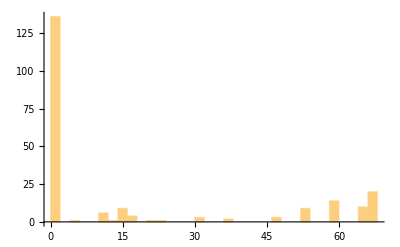
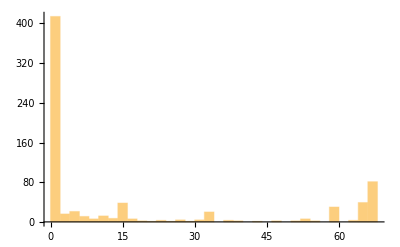

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Show[Histogram[slopesFullRW[[i]], 3]], {i, 1, Length[initStates] }]
```

```mathematica
rulesApprovedNoNull = ReadList["rulesApprovedNoNull.txt"];
```

```mathematica
slopesFullRW=ParallelTable[calcSlopeFullRW[i,j,rulesApprovedNoNull,rules,initStates],{i,1,Length[initStates]},{j,1, 10}];
```